```mathematica
Quit[]
```

```mathematica
INT[w_,mu_,ar_,l_,m_,s_,NITMAX_]:=(
M=1;
br=Sqrt[1-ar^2];
rminus=(1-br);
rplus=1+br;
k1=1/2*Abs[m-s];
k2=1/2*Abs[m+s];
OmegaH=ar/(2*M*rplus);
Alm=SpheroidalEigenvalue[l,m,I ar √(w^2-mu^2)]-ar^2 (w^2-mu^2);

Clear[α,β,γ];
q=-Sqrt[mu^2-w^2];
c0=1-2*I*w-2*I/br*(w-ar*m/2);
c1=-4+4*I*(w-I*q*(1+br))+4*I/br*(w-ar*m/2)-2*(w^2+q^2)/q;
c2=3-2*I*w-2*I/br*(w-ar*m/2)-2*(q^2-w^2)/q;c3=2*I*(w-I*q)^3/q+2*(w-I*q)^2*br+q^2*ar^2+2*I*q*ar*m-Alm-1-(w-I*q)^2/q+2*q*br+2*I/br*((w-I*q)^2/q+1)*(w-ar*m/2);c4=(w-I*q)^4/q^2+2*I*w*(w-I*q)^2/q-2*I/br*(w-I*q)^2/q*(w-ar*m/2);γ=Function[n,n^2+(c2-3)*n+c4+(-c2+2)*0];
β=Function[n,-2*n^2+(c1+2)*n+c3];
α=Function[n,n^2+(c0+1)*n+c0];

Leaver31=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>0,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];

β[0]/α[0]-Leaver31
)
```

```mathematica
INT[(*w*)0.29-0.09*I,(*mu*)0.2,(*ar*)0.5,(*l*)1,(*m*)1,(*s*)0,(*NITMAX*)500]
```

-1.53526-2.50005 ⅈ

#### fundamental 0.1

```mathematica
mu0=0.1;
a0=0;
l0=2;
m0=2;
N0=1000;
wguess=0.09987363876795732-1.3356306200190647*^-11 ⅈ;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.0999442+1.44713×10^-15 ⅈ,2.95297×10^-9}

```mathematica
ωn1=0.0998736387689641-1.3356454256383495*^-11 ⅈ;
```

#### Wavefunction fundamental 0.1

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(r-rplus)^(-I*sigma)*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

General::munfl: 0.214245^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.21424^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.214245^999 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

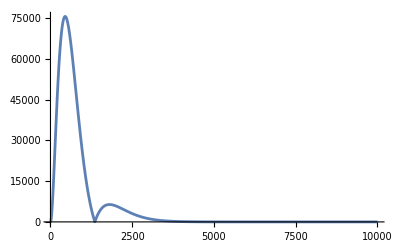

```mathematica
Plot[{Abs[Rpsi*r]},{r,2.01,10000}, PlotRange->All]
```

```mathematica
Rn1=Rpsi*r;
```

```mathematica
Rn1Hydro= √((2 0.1 0.1/2)^3 1/(4(3 2)))(2 0.1 0.1 r/2)^1 Exp[- 0.1 0.1 r/2]LaguerreL[0,3, 2 0.1 0.1 r/2]
```

2.04124×10^-6 ⅇ^(-0.005 r) r

General::munfl: 0.0203877^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0203877^999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0203877^998 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

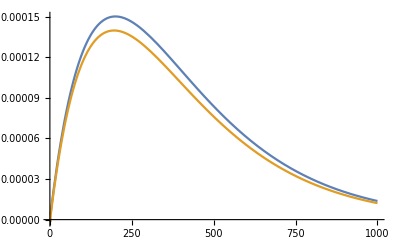

```mathematica
Plot[{Rn1Hydro, Rn1/(771500*r)//Re},{r,2,1000}, PlotRange->All]
```

#### overtone n=1 0.1

```mathematica
mu0=0.1;
a0=0.9;
l0=0;
m0=0;
N0=1000;
wguess=0.09994392293552769-4.7204207476751675*^-12 ⅈ;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.0999421-4.9171×10^-7 ⅈ,2.05991×10^-10}

```mathematica
ωn2=0.0999439463894689+2.4199843638664814*^-12 ⅈ;
```

#### Wavefunction overtone n=1 0.1

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(r-rplus)^(-I*sigma)*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

```mathematica
ae[3]
```

0.0427409+0.039981 ⅈ

```mathematica
SpheroidalEigenvalue[1,1,I a0 √(w^2-m0^2)]-a0^2 (w^2-m0^2)/.w->root
```

2.1575-7.55719×10^-14 ⅈ

General::munfl: 1.31968×10^-215 (2.66577×10^-128+1.66418×10^-128 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.16446×10^-215 (3.46943×10^-128+2.16589×10^-128 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.55×10^-215 (4.51535×10^-128+2.81883×10^-128 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

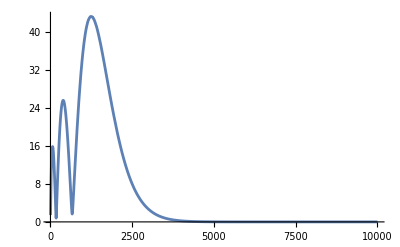

```mathematica
Plot[{Abs[Rpsi*r]},{r,2.0000,10000}, PlotRange->All]
```

```mathematica
Rn2=Rpsi*r;
```

#### overtone n=2 0.1

```mathematica
mu0=0.1;
a0=0.9;
l0=0;
m0=0;
N0=1000;
wguess=0.09996392293552769-4.7204207476751675*^-12 ⅈ;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.0999677-2.04944×10^-7 ⅈ,1.71112×10^-10}

```mathematica
ωn2=0.09996850531241268-2.1078879046090942*^-12 ⅈ;
```

#### Wavefunction overtone n=2 0.1

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(r-rplus)^(-I*sigma)*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

General::munfl: 1.31968×10^-215 (-7.98911×10^-131-4.9006×10^-131 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.16446×10^-215 (-1.03975×10^-130-6.37795×10^-131 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.55×10^-215 (-1.35318×10^-130-8.30054×10^-131 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

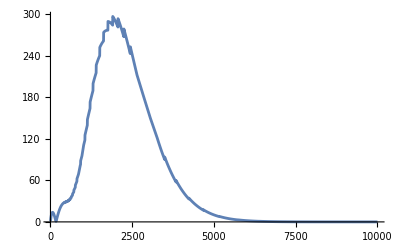

```mathematica
Plot[{Abs[Rpsi*r]},{r,2.0000,10000}, PlotRange->All]
```

```mathematica
Rn2=Rpsi*r;
```

#### overtone n=3 0.1

```mathematica
mu0=0.1;
a0=0;
l0=1;
m0=1;
N0=5000;
wguess=0.09997603137398303-6.433603246656939*^-13 ⅈ;

f[x_?NumberQ]:=INT[x,mu0,a0,l0,m0,0,N0];
root=x/.FindRoot[f[x],{x,wguess}];
check=Abs[f[root]];
{root,check}
```

{0.0999799-1.10141×10^-12 ⅈ,2.11895×10^-10}

```mathematica
ωn4=0.09997986719996103-1.1014054882587737*^-12 ⅈ;
```

#### Wavefunction overtone n=3 0.1

```mathematica
ae[0]=1;
ae[1]=-β[0]/α[0]/.w->root;
i=1;While[i<N0,ae[i+1]=(-β[i]*ae[i]-γ[i]*ae[i-1])/(α[i])/.w->root;i=i+1];
```

```mathematica
chi=(mu0^2-2*w^2)/q/.w->root;
sigma=2*rplus*(w-m0*a0/(2*M*rplus))/(rplus-rminus)/.w->root;
Rpsi=(r-rplus)^(-I*sigma)*(r-rminus)^(I*sigma+chi-1)*Exp[q*r]*Sum[ae[n]*(r-rplus)^n/(r-rminus)^n,{n,0,N0}];
```

General::munfl: 0.204245^5000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.20424^5000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.204245^4999 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

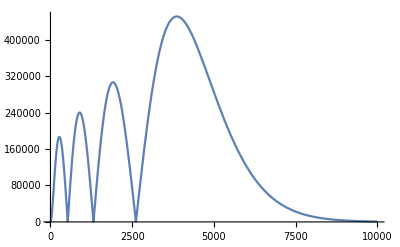

```mathematica
Plot[{Abs[Rpsi*r]},{r,2.0000,10000}, PlotRange->All]
```

```mathematica
Rn4=Rpsi*r;
```